# Cuestionario: Aproximación de raíces con Mathematica.

1. Observa gráficamente que la función F(x) = x^2 − Cos[x] + Sin[x] posee un mínimo en el intervalo [−0.5, −0.125]. Partiendo de este intervalo, ¿cuántas iteraciones son necesarias para obtener mediante el método de bisección, un intervalo de longitud menor que 10^-2 que contenga a la raíz? Calcula todas las iteraciones necesarias, así como el valor aproximado para el punto donde se alcanza el mínimo.

Vamos a utilizar la fórmula (1)  del tutorial de la práctica
                                                                                (|b-a|)/2^(n+1)< ε                                                                          (1)
                                                                                
Tendremos que resolver la ecuación  (|b-a|)/2^(n+1)=(|0.125-(-0.5)|)/2^(n+1)<10^-2

```mathematica
Simplify[Abs[-0.125-(-0.5)]/2^(n+1)]
```

0.1875 2^-n

```mathematica
Reduce[0.1875 2^-n< 10^-2,n, Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n>4.22882

El número de bisecciones necesario será 5. Vamos a obtenerlas:

Como tenemos que estudiar los ceros de la derivada, vamos a derivar la función y representar  gráficamente la función para ver que efectivamente tiene un mínimo:

```mathematica
D[x^2-Cos[x]+ Sin[x],x]
```

2 x+Cos[x]+Sin[x]

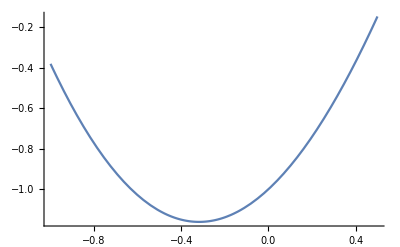

```mathematica
Plot[x^2-Cos[x]+ Sin[x],{x,-1,0.5}]
```

Vamos a utilizar las funciones desarrolladas en el tutorial:

```mathematica
Biseccion[f_, {a_,b_,n_}]:=SetPrecision[Module[{an,bn,xn}, an=a;bn=b;
For[i=1, i≤ n, i++, xn=(an+bn)/2;

If[Limit[f[x], x->xn]==0,xn,
If[Sign[f[xn]* f[an]]==-1,bn=xn,an=xn]]];
xn],50]
```

```mathematica
f[x_]:=2 x+Cos[x]+Sin[x]
```

```mathematica
Biseccion[f, {-0.5,-0.125,5}]
```

-0.32421875

El resultado será:

La aproximación en el caso de la bisección nos da el resultado de  x=-0.324218750

2 .	Aplica el método de Newton para hallar una aproximación con 15 decimales correctos, del primer punto de corte de la funcion  F(x) = 2 x+Cos[x]+Sin[x] en el intervalo [−1,−0.2]. Utiliza como estimación inicial el valor x=-1.

Aplicamos el método de Newton utilizando la misma estrategia que la del tutorial de la práctica:

Definimos primero la función que vamos a utilizar:

```mathematica
f[x_]:=2 x+Cos[x]+Sin[x]
```

Comprobamos que tenemos un cero cerca de -1:

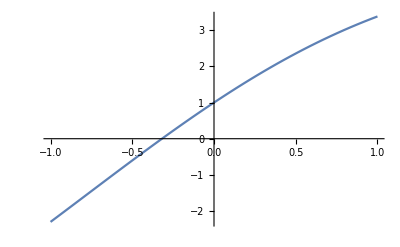

```mathematica
Plot[2 x+Cos[x]+Sin[x],{x,-1,1}]
```

Cargamos la  función que vamos a utilizar del tutorial:

```mathematica
NewtonP[f_, x0_,pres_]:=SetPrecision[Module[{xn,error, i},
xn= x0;
error=100;
i=0;
While[error>pres, {
xn1=N[xn-(f[xn]/f'[xn]),50   ];
error=N[Abs[xn1-xn],50];
xn=xn1;
i=i+1;
Print["Iteración:",i,"    x=", N[xn1,50]  , "    error= ", error]  
}  ];
],50]
```

```mathematica
NewtonP[f, -1, 10^(-15)]
```

Iteración:1    x=-0.31953786337944027708632495867682496883254169546414    error= 0.68046213662055972291367504132317503116745830453586

Iteración:2    x=-0.3183664590873559483063591176622283878949003903306    error= 0.0011714042920843287799658410145965809376413051336

Iteración:3    x=-0.3183663254026427492772557345733064069962199466255    error= 1.33684713199029103383088921980898680443705×10^-7

Iteración:4    x=-0.3183663254026410054439954519194367526617744021256    error= 1.7438332602826538696543344455445×10^-15

Iteración:5    x=-0.318366325402641005443995451919140029498902539421    error= 2.96723162871862705×10^-31